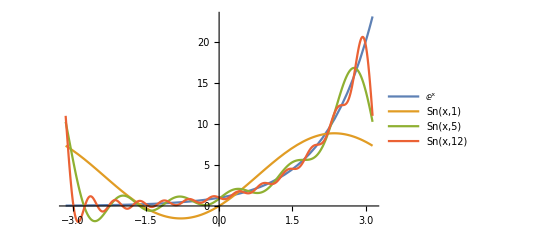

```mathematica
ClearAll["Global`*"]
Sn[x_,k_]:=Sinh[π]/π(1+2∑_(n=1)^k ((-1)^n/(n^2+1))(Cos[n x] - n Sin[n x]))
Plot[{ⅇ^x, Sn[x,1], Sn[x,5], Sn[x,12]}, {x, -π, π}, PlotLegends-> "Expressions" ]
```

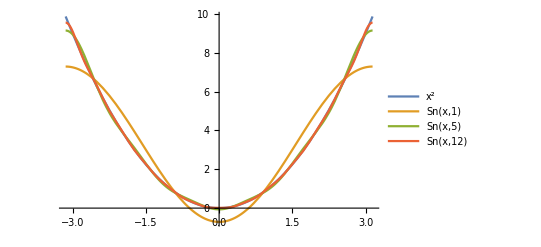

```mathematica
ClearAll["Global`*"]
Sn[x_,k_]:=π^2/3+4∑_(n=1)^k (-1)^n/n^2 Cos[n x]
Plot[{x^2, Sn[x,1], Sn[x,5], Sn[x,12]}, {x, -π, π}, PlotLegends-> "Expressions" ]
```

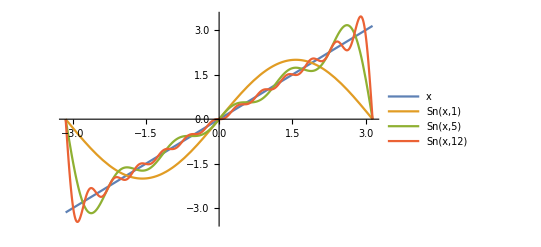

```mathematica
ClearAll["Global`*"]
Sn[x_,k_]:=2∑_(n=1)^k (-1)^(n+1)/n Sin[n x]
Plot[{x, Sn[x,1], Sn[x,5], Sn[x,12]}, {x, -π, π}, PlotLegends-> "Expressions" ]
```

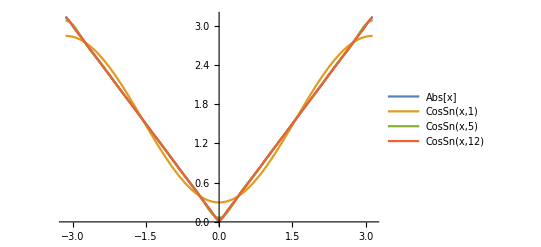

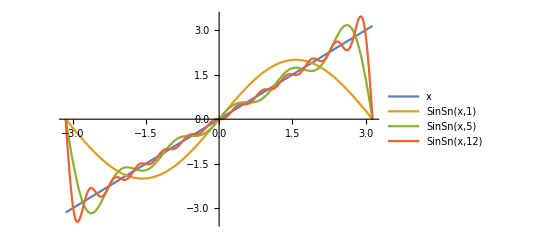

```mathematica
ClearAll["Global`*"]
CosSn[x_,k_]:=π/2-4/π∑_(n=1)^k Cos[(2n-1)x]/(2n-1)^2
SinSn[x_,k_]:=2∑_(n=1)^k (-1)^(n+1)/n Sin[n x]
Plot[{Abs[x], CosSn[x,1], CosSn[x,5], CosSn[x,12]}, {x, -π, π}, PlotLegends-> "Expressions" ]
Plot[{x, SinSn[x,1], SinSn[x,5], SinSn[x,12]}, {x, -π, π}, PlotLegends-> "Expressions" ]
```